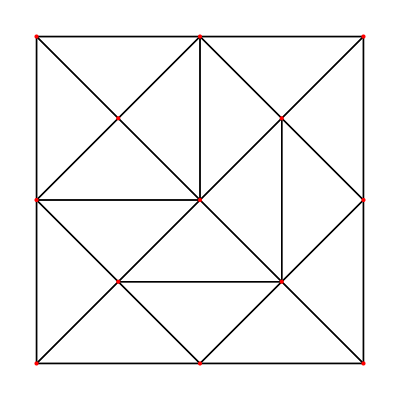

```mathematica
p0={{0.,0.},{0.5,0.},{1.,0.},{0.25,0.25},{0.75,0.25},{0.,0.5},{0.5,0.5},{1.,0.5},{0.25,0.75},{0.75,0.75},{0.,1.},{0.5,1.},{1.,1.}};
(*Do[p0[[i,1]]=RandomReal[{0,bboxL}];
p0[[i,2]]=RandomReal[{0,bboxH}];,{i,Nnodes}];*)

Needs["ComputationalGeometry`"];
dt=DelaunayTriangulation[p0];
(*toPairs[{m_,ns_List}]:=Map[{m,#}&,ns];
edges=Flatten[Map[toPairs,dt],1];*)
Graphics[GraphicsComplex[p0,{Line[edges],Red,PointSize[Medium],Point[p0]}]]
```